```mathematica
a=0; b=6;n=4;
h=(b-a)/n;
XDT={}; YDT={};
For[i=0,i<=n,i++,
xdata[i]=a+i×h;
ydata[i]=N[Exp[2xdata[i]-2 xdata[i]^2/7]*ArcTan[3 xdata[i]^5/14+5/6]];
XDT=Append[XDT,xdata[i]];
YDT=Append[YDT,ydata[i]];];
Array[xdata,{n+1,0}];Array[ydata,{n+1,0}];
ex=∑_(i=0)^n xdata[i];ey=∑_(i=0)^n ydata[i];exx=∑_(i=0)^n xdata[i]^2;
exy=∑_(i=0)^n xdata[i]*ydata[i];
eyy=∑_(i=0)^n ydata[i]^2;
a=(ey*exx-ex*exy)/((n+1)*exx-ex^2);b=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
g[x_]:=a+b*x;
g[x]
```

13.2477+2.83756 x

```mathematica
For[i=0,i<=n,i++,xdata[i]=XDT[[i+1]];
ydata[i]=YDT[[i+1]]];
pln=∑_(i=0)^n ydata[i]*∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
```

0.694738-30.0595 x+38.6707 x^2-10.0347 x^3+0.74362 x^4

{{0.,0.694738},{1.5,12.5121},{3.,47.849},{4.5,39.0273},{6.,8.71884}}

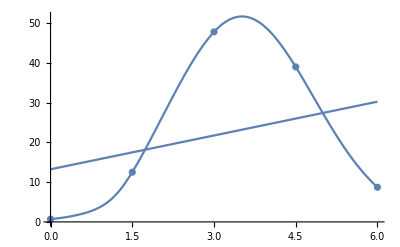

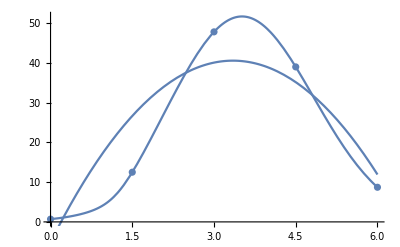

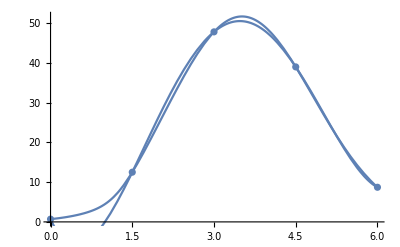

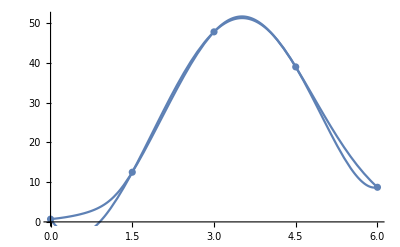

{{0.,0.694738},{0.6,2.11037},{1.2,6.85994},{1.8,19.8499},{2.4,35.5054},{3.,47.849},{3.6,51.616},{4.2,45.1195},{4.8,32.0584},{5.4,18.5322},{6.,8.71884}}

```mathematica
data=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]
Clear[a,b];
rules=FindFit[data,a+b*x,{a,b,c},x];y=a+b*x/.rules;
rules1=FindFit[data,a+b*x+c*x^2,{a,b,c},x];y1=a+b*x+c*x^2/.rules1;
rules2=FindFit[data,a+b*x+c*x^2+d*x^3+e*x^4,{a,b,c,d,e},x];y2=a+b*x+c*x^2+d*x^3+e*x^4/.rules2;
rules3=FindFit[data,a+b*x+c*x^2+d*x^3+e*x^4+f*x^5,{a,b,c,d,e,f},x];y3=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5/.rules3;
gr1:=Plot[N[Exp[2x-2 x^2/7]*ArcTan[3 x^5/14+5/6]],{x,0,6}];
gr2:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
gr3:=Plot[y,{x,0,6}];
gr4:=Plot[y1,{x,0,6}];
gr5:=Plot[y2,{x,0,6}];
gr6:=Plot[y3,{x,0,6}];
Show[{gr1,gr2,gr3}]
Show[{gr1,gr2,gr4}]
Show[{gr1,gr2,gr5}]
Show[{gr1,gr2,gr6}]
```

```mathematica
r=((n+1)*exy-ex*ey)/(√((n+1)*exx-ex^2)*√((n+1)*eyy-ey^2))
```

0.340156

Show::gcomb: Could not combine the graphics objects in Show[{gr1, gr2, gr3}].